Dynamic simulation of three-wheeled omnidirectional mobile robot

```mathematica
NotebookSave[]
```

```mathematica
Clear["Global`*"];
```

## Section I.

### Configuration definition

#### Global coordinate system definition

```mathematica
ux={1,0,0};
uy={0,1,0};
uz={0,0,1};
rO={0,0,0};
```

#### Basic coordinate system definition

```mathematica
φA=π/6; φB=φA+(2π)/3;φC=φB+(2π)/3;
```

```mathematica
uxA=RotationMatrix[φA,{0,0,1}].ux;
uxB=RotationMatrix[φB,{0,0,1}].ux;
uxC=RotationMatrix[φC,{0,0,1}].ux;
uyA=RotationMatrix[φA,{0,0,1}].uy;
uyB=RotationMatrix[φB,{0,0,1}].uy;
uyC=RotationMatrix[φC,{0,0,1}].uy;
uzA=Cross[uxA,uyA];
uzB=Cross[uxB,uyB];
uzC=Cross[uxC,uyC];
```

### Geometry parameters

#### Wheel definition

```mathematica
wheelCircleRadius=0.12;
wheelRadius=0.03;
wheelWidth=0.0050;
mWheel =0.060;
A=({{-Sin[φA], Cos[φA], wheelCircleRadius}, {-Sin[φB], Cos[φB], wheelCircleRadius}, {-Sin[φC], Cos[φC], wheelCircleRadius}});
```

```mathematica
rA=wheelCircleRadius uxA;
rB=wheelCircleRadius uxB;
rC=wheelCircleRadius uxC;
wheelθMeasured = 0.012099670934420;
```

```mathematica
1520
```

1520

#### Case definition

```mathematica
ρ=1000;
mTriangleCase = 0.184;
mMotor =0.200;
mOthers =0.6;
offsetLength1=0.04;
offsetLength2= offsetLength1+0.05;
wheelCircleRadiusRatio =0.8;
dummyCaseRadius=wheelCircleRadiusRatio wheelCircleRadius;
dummyCaseHeight=0.05;
r1={0,0,offsetLength1};
r2={0,0,offsetLength2};
mCase=mTriangleCase +3×mMotor+mOthers

cmCase = (mTriangleCase( r1 + r2)+3×mMotor rO+ (r1 + r2 )mOthers)/mCase
```

1.384

{0.,0.,0.0736416}

#### Package definition

```mathematica
ρ=2500;
packageHeight = 0.1;
packageRadius=0.5 dummyCaseRadius;
cmPackage=r2+{0,0,packageHeight/2};
mPackage=packageRadius^2 π packageHeight ρ
```

1.80956

```mathematica
ρ=7800;rodHeight = 1; rodDiameter = 0.010;mRod=(rodDiameter/2)^2 π rodHeight ρ;cmRod=r2+{0,0,rodHeight/2};
```

```mathematica
ρ=6500;diskHeight = 0.01; diskDiameter = 0.100;mDisk=(diskDiameter/2)^2 π diskHeight ρ;mDisk=0.50;
cmDisk=r2+{0,0,rodHeight};
```

#### Common mass center

```mathematica
cmC=cmCase
```

{0.,0.,0.0736416}

```mathematica
cmC=(cmCase mCase+cmPackage mPackage)/(mCase+mPackage);
cmC=(cmCase mCase+cmRod mRod+cmDisk mDisk)/(mCase+mRod+mDisk)
```

{0.,0.,0.403892}

```mathematica
g=9.81;
```

#### Case

```mathematica
a={ax,ay,0};ϵ={0,0,ϵz};v={vx,vy,0};ω={0,0,ωz};
KA={KAx,KAy,KAz};KB={KBx,KBy,KBz};KC={KCx,KCy,KCz};
G={0,0,-mRobot g};
```

```mathematica
θTriangle = (mTriangleCase wheelCircleRadius^2)/3;θCase = 2 θTriangle;
```

```mathematica
θPackage=1/2 mPackage dummyCaseRadius;
```

```mathematica
θRod=1/2 mRod (rodDiameter/2);
```

```mathematica
θDisk=1/2 mDisk (diskDiameter/2)^2;
```

```mathematica
θMotorA = mMotor Norm[(cmC-rA)];
θMotorB = mMotor Norm[(cmC-rB)];
θMotorC = mMotor Norm[(cmC-rC)];
θMotors = θMotorA+θMotorB+θMotorC;
```

```mathematica
eq1=mRobot a== KA+KB+KC+G
```

{ax mRobot,ay mRobot,0}=={KAx+KBx+KCx,KAy+KBy+KCy,KAz+KBz+KCz-9.81 mRobot}

```mathematica
eq2=θRobot ϵ==Cross[rA-cmC,KA]+Cross[rB-cmC,KB]+Cross[rC-cmC,KC]+ 0 MA uxA/100+ 0 MB uxB/100+0 MC uxC/100
```

{0,0,ϵz θRobot}=={0.303756 KAy+0.06 KAz+0.303756 KBy+0.06 KBz+0.303756 KCy-0.12 KCz,0.-0.303756 KAx-0.103923 KAz-0.303756 KBx+0.103923 KBz-0.303756 KCx,0.-0.06 KAx+0.103923 KAy-0.06 KBx-0.103923 KBy+0.12 KCx}

#### Wheels

```mathematica
kA=-RotationMatrix[-φA,{0,0,1}].KA;
kB=-RotationMatrix[-φB,{0,0,1}].KB;
kC=-RotationMatrix[-φC,{0,0,1}].KC;
```

```mathematica
aA={aAx,aAy,0};ϵA={ϵAx,0,0};vA={vAx,vAy,0};ωA={ωAx,0,0};
aB={aBx,aBy,0};ϵB={ϵBx,0,0};vB={vBx,vBy,0};ωB={ωBx,0,0};
aC={aCx,aCy,0};ϵC={ϵCx,0,0};vA={vCx,vCy,0};ωC={ωCx,0,0};
G={0,0,-mWheel g};
SA=sA {0,1,0};SB=sB {0,1,0};SC=sC {0,1,0};NA=nA {0,0,1};NB=nB {0,0,1};NC=nC {0,0,1};
```

```mathematica
θWheel=wheelθMeasured;
```

```mathematica
eq1A=mWheel aA== kA+sA {0,1,0}+G+NA;
eq1B=mWheel aB== kB+sB {0,1,0}+G+NB;
eq1C=mWheel aC== kC+sC {0,1,0}+G+NC;
```

```mathematica
eq2A=θWheel ϵAx==-MA+wheelRadius sA;
eq2B=θWheel ϵBx==-MB+wheelRadius sB;
eq2C=θWheel ϵCx==-MC+wheelRadius sC;
```

#### Constraints

2D rolling

```mathematica
(*No slip condition in yWheel direction*)
rollingY={aAy,aBy,aCy}==-wheelRadius{ϵAx,ϵBx,ϵCx};
```

Rigid body connection between wheels and the case

```mathematica
rigidBodyA=aA==RotationMatrix[-φA,{0,0,1}].(a+Cross[ϵ,rA]+Cross[ω,Cross[ω,rA]])//Chop//FullSimplify;
rigidBodyB=aB==RotationMatrix[-φB,{0,0,1}].(a+Cross[ϵ,rB]+Cross[ω,Cross[ω,rB]])//Chop//FullSimplify;
rigidBodyC=aC==RotationMatrix[-φC,{0,0,1}].(a+Cross[ϵ,rC]+Cross[ω,Cross[ω,rC]])//Chop//FullSimplify;
```

#### Electromechanical equations

```mathematica
g=9.81;
```

```mathematica
θ=0.012099670934420;
b=0.019715497097366;
K=0.824871094407238;
R=7.975905973570620;
L=0.0;
V=12;
SPEED=0;
TLOAD = cR LOAD/3 g;
```

```mathematica
Clear[V];Clear[SPEED];Clear[cR];
```

```mathematica
MomentEquation = θ x'[t] +b x[t] == K y[t]-TLOAD;
KirchoffEquation = L y'[t]+R y[t] ==V-K x[t];
```

```mathematica
CombinedEquation = MomentEquation/.Solve[KirchoffEquation,y[t]][[1]]//Simplify
```

1. cR LOAD+0.0321174 x[t]+0.00370021 x'[t]==0.031627 V

```mathematica
solution = DSolve[{CombinedEquation,x[0]==SPEED},x[t],t];
```

```mathematica
RotationalSpeedAnalytic = x[t]/.solution[[1]]//Simplify;
```

```mathematica
GetRotationalSpeed[t_,V_,SPEED_,LOAD_,cR_]= x[t]/.DSolve[{CombinedEquation,x[0]==SPEED},x[t],t][[1]]//Simplify
```

ⅇ^(-8.6799 t) (cR (31.1358-31.1358 ⅇ^(8.6799 t)) LOAD+1. SPEED+(-0.984731+0.984731 ⅇ^(8.6799 t)) V)

```mathematica
ArmatureCurrentAnalytic = y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.solution[[1]]//Simplify;
```

```mathematica
TorqueAnalytic = K y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.solution[[1]]//Simplify;
```

```mathematica
VoltageToTorque[t_,V_,SPEED_,LOAD_,cR_]= K y[t]/.Solve[KirchoffEquation,y[t]][[1]]/.DSolve[{MomentEquation/.Solve[KirchoffEquation,y[t]][[1]],x[0]==SPEED},x[t],t][[1]]//Simplify
```

ⅇ^(-8.6799 t) (cR (-2.65614+2.65614 ⅇ^(8.6799 t)) LOAD-0.0853085 SPEED+(0.0840059+0.0194145 ⅇ^(8.6799 t)) V)

```mathematica
(*TR=RollingFrictionTorque =x/.Solve[GetRotationalSpeed[5,12,0,x]==0.9854 GetRotationalSpeed[5,12,0,0],x][[1]]*)
```

```mathematica
(*cR= TR/(3.187/3 g)*)
```

```mathematica
coeff = x/.Solve[GetRotationalSpeed[5,12,0,0,x] 0.9778==GetRotationalSpeed[5,12,0,4.213,x],x][[1]]
```

0.00199987

```mathematica
GetRotationalSpeed[5,12,0,4.2,coeff]/GetRotationalSpeed[5,12,0,0,coeff]
```

0.977869

```mathematica
whatIsMass[MeasuredVelocity_]:=m/.Solve[GetRotationalSpeed[5,12,0,m,coeff]==MeasuredVelocity,m][[1]]
```

```mathematica
whatIsMass[11.5]
```

5.0873

```mathematica
Manipulate[
Plot[GetRotationalSpeed[t,voltage,speed,mass,coeff],{t,0,2},PlotRange->{0,13},PlotTheme->"Scientific"],
{{time,5},0,5},
{{voltage,12},0,12},
{{speed,0},-12,12},
{{mass,0},0,5}
];
```

```mathematica
Manipulate[Plot[VoltageToTorque[t,12,0,mass,coeff],{t,0,2},PlotRange->{0,2}],{mass,0,10}];
```

```mathematica
GetRotationalSpeed[5,12,0,2,coeff]
```

11.6922

#### Solve with numerical values

```mathematica
mRobot=mCase+mPackage;mRobot=mCase+mRod+mDisk;
θRobot=θCase+θPackage;θRobot=θCase+θRod+θDisk; 
ωz=0;
{UA,UB,UC}=12 A.{0,1,0*1/wheelCircleRadius}
{MA,MB,MC}={VoltageToTorque[0,UA,0,mRobot,0],VoltageToTorque[0,UB,0,mRobot,0],VoltageToTorque[0,UC,0,mRobot,0]}
```

{10.3923,-10.3923,0.}

{1.07478,-1.07478,0.}

```mathematica
{eq1,eq2,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY}//Column//Chop//FullSimplify//N
```

{2.49661 ax,2.49661 ay,0.}=={KAx+KBx+KCx,KAy+KBy+KCy,-24.4917+KAz+KBz+KCz}
{0.,0.,0.00392293 ϵz}=={0.303756 KAy+0.06 KAz+0.303756 KBy+0.06 KBz+0.303756 KCy-0.12 KCz,-0.303756 KAx-0.103923 KAz-0.303756 KBx+0.103923 KBz-0.303756 KCx,-0.06 KAx+0.103923 KAy-0.06 KBx-0.103923 KBy+0.12 KCx}
{0.06 aAx+0.866025 KAx+0.5 KAy,0.06 aAy-0.5 KAx+0.866025 KAy-1. sA,0.5886+KAz-1. nA}=={0.,0.,0.}
{0.06 aBx-0.866025 KBx+0.5 KBy,0.06 aBy-0.5 KBx-0.866025 KBy-1. sB,0.5886+KBz-1. nB}=={0.,0.,0.}
{0.06 aCx,0.06 aCy,0.}=={KCy,-1. KCx+sC,-0.5886-1. KCz+nC}
1. sA==35.8259+0.403322 ϵAx
35.8259+1. sB==0.403322 ϵBx
1. sC==0.403322 ϵCx
{aAx,aAy,0.}=={0.866025 ax+0.5 ay,-0.5 ax+0.866025 ay+0.12 ϵz,0.}
{aBx,aBy,0.}=={-0.866025 ax+0.5 ay,-0.5 ax-0.866025 ay+0.12 ϵz,0.}
{aCx,aCy,0.}=={-1. ay,ax+0.12 ϵz,0.}
{aAy,aBy,aCy}=={-0.03 ϵAx,-0.03 ϵBx,-0.03 ϵCx}

```mathematica
solutions=First@Solve[{eq1,eq2,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY},{ax,ay,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aBx,aBy,aCx,aCy,ϵAx,ϵBx,ϵCx}];
solutions//MatrixForm//FullSimplify
```

(ax→0.
ay→2.7165
ϵz→3.99604×10^-16
KAx→-2.09896
KBx→2.09896
KCx→-8.1499×10^-16
KAy→3.47251
KBy→3.47251
KCy→-0.16299
KAz→2.44146
KBz→2.44146
KCz→19.6088
nA→3.03006
nB→3.03006
nC→20.1974
sA→4.19792
sB→-4.19792
sC→-8.12112×10^-16
aAx→1.35825
aAy→2.35256
aBx→1.35825
aBy→-2.35256
aCx→-2.7165
aCy→4.79525×10^-17
ϵAx→-78.4185
ϵBx→78.4185
ϵCx→-1.59842×10^-15)

```mathematica
ParametricAcceleration=ay/.solutions[[2]]//FullSimplify//Chop
```

2.7165

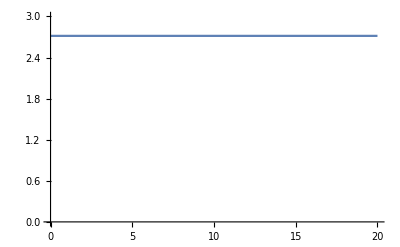

```mathematica
Plot[ParametricAcceleration,{X,0,20},PlotRange->{0,3}]
```

```mathematica
solutions=First@Solve[{
eq1[[1]][[1]]==eq1[[2]][[1]],
eq1[[1]][[2]]==eq1[[2]][[2]],
eq1[[1]][[3]]==eq1[[2]][[3]],
eq2[[1]][[1]]==eq2[[2]][[1]],
eq2[[1]][[2]]==eq2[[2]][[2]],
eq2[[1]][[3]]==eq2[[2]][[3]],
eq1A[[1]][[1]]==eq1A[[2]][[1]],
eq1A[[1]][[2]]==eq1A[[2]][[2]],
eq1A[[1]][[3]]==eq1A[[2]][[3]],
eq1B[[1]][[1]]==eq1B[[2]][[1]],
eq1B[[1]][[2]]==eq1B[[2]][[2]],
eq1B[[1]][[3]]==eq1B[[2]][[3]],
eq1C[[1]][[1]]==eq1C[[2]][[1]],
eq1C[[1]][[2]]==eq1C[[2]][[2]],
eq1C[[1]][[3]]==eq1C[[2]][[3]],
eq2A,eq2B,eq2C,
rigidBodyA[[1]][[1]]==rigidBodyA[[2]][[1]],
rigidBodyA[[1]][[2]]==rigidBodyA[[2]][[2]],
rigidBodyB[[1]][[1]]==rigidBodyB[[2]][[1]],
rigidBodyB[[1]][[2]]==rigidBodyB[[2]][[2]],
rigidBodyC[[1]][[1]]==rigidBodyC[[2]][[1]],
rigidBodyC[[1]][[2]]==rigidBodyC[[2]][[2]],
rollingY[[1]][[1]]==rollingY[[2]][[1]],
rollingY[[1]][[2]]==rollingY[[2]][[2]],
rollingY[[1]][[3]]==rollingY[[2]][[3]]
},{ax,ay,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aBx,aBy,aCx,aCy,ϵAx,ϵBx,ϵCx}];
solutions//MatrixForm;
```

```mathematica
Coefficients=CoefficientArrays[{
eq1[[1]][[1]]==eq1[[2]][[1]],
eq1[[1]][[2]]==eq1[[2]][[2]],
eq1[[1]][[3]]==eq1[[2]][[3]],
eq2[[1]][[1]]==eq2[[2]][[1]],
eq2[[1]][[2]]==eq2[[2]][[2]],
eq2[[1]][[3]]==eq2[[2]][[3]],
eq1A[[1]][[1]]==eq1A[[2]][[1]],
eq1A[[1]][[2]]==eq1A[[2]][[2]],
eq1A[[1]][[3]]==eq1A[[2]][[3]],
eq1B[[1]][[1]]==eq1B[[2]][[1]],
eq1B[[1]][[2]]==eq1B[[2]][[2]],
eq1B[[1]][[3]]==eq1B[[2]][[3]],
eq1C[[1]][[1]]==eq1C[[2]][[1]],
eq1C[[1]][[2]]==eq1C[[2]][[2]],
eq1C[[1]][[3]]==eq1C[[2]][[3]],
eq2A,eq2B,eq2C,
rigidBodyA[[1]][[1]]==rigidBodyA[[2]][[1]],
rigidBodyA[[1]][[2]]==rigidBodyA[[2]][[2]],
rigidBodyB[[1]][[1]]==rigidBodyB[[2]][[1]],
rigidBodyB[[1]][[2]]==rigidBodyB[[2]][[2]],
rigidBodyC[[1]][[1]]==rigidBodyC[[2]][[1]],
rigidBodyC[[1]][[2]]==rigidBodyC[[2]][[2]],
rollingY[[1]][[1]]==rollingY[[2]][[1]],
rollingY[[1]][[2]]==rollingY[[2]][[2]],
rollingY[[1]][[3]]==rollingY[[2]][[3]]
},{ax,ay,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aBx,aBy,aCx,aCy,ϵAx,ϵBx,ϵCx}]
```

{SparseArray[…],SparseArray[…]}

```mathematica
b=-Coefficients[[1]];A=Coefficients[[2]];
```

```mathematica
A//MatrixForm
```

(2.49661 | 0 | 0 | -1. | -1. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2.49661 | 0 | 0 | 0 | 0 | -1. | -1. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | -1. | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.303756 | -0.303756 | -0.303756 | -0.06 | -0.06 | 0.12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.303756 | 0.303756 | 0.303756 | 0 | 0 | 0 | 0.103923 | -0.103923 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.00392293 | 0.06 | 0.06 | -0.12 | -0.103923 | 0.103923 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.866025 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.06 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.5 | 0 | 0 | 0.866025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0.06 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.866025 | 0 | 0 | 0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.06 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.5 | 0 | 0 | -0.866025 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0.06 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.06 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0.06 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | -1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.03 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0120997 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.03 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0120997 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.03 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0120997
-0.866025 | -0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.5 | -0.866025 | -0.12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.866025 | -0.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0.5 | 0.866025 | -0.12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
-1. | 0 | -0.12 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0.03 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0.03 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0.03)

```mathematica
invA=Inverse[A]
```

{{0.0437776,2.18188×10^-17,0.,0.,0.,2.61553×10^-16,0.0379125,-0.0218888,0.,-0.0379125,-0.0218888,0.,-2.18188×10^-17,0.0437776,0.,0.729627,0.729627,-1.45925,-0.00227475,0.295588,0.00227475,0.295588,7.85766×10^-19,-0.591176,-0.294275,-0.294275,0.58855},{-8.77253×10^-17,0.0437776,0.,0.,0.,1.93318×10^-16,0.0218888,0.0379125,0.,0.0218888,-0.0379125,0.,-0.0437776,-6.92939×10^-17,0.,-1.26375,1.26375,-9.63225×10^-17,-0.00131333,-0.511974,-0.00131333,0.511974,0.00262666,-1.58884×10^-16,0.509699,-0.509699,3.80071×10^-17},{-1.16032×10^-16,-1.00633×10^-16,0.,0.,0.,1.70271,3.79047×10^-17,0.204325,0.,-3.79047×10^-17,0.204325,0.,1.00633×10^-16,0.204325,0.,-6.81084,-6.81084,-6.81084,-1.67771×10^-19,-2.75922,4.50458×10^-18,-2.75922,-6.45027×10^-18,-2.75922,2.74696,2.74696,2.74696},{-0.149764,0.254849,0.,0.,0.,1.37961,0.863751,-0.0388585,0.,0.257124,0.0197293,0.,-0.254849,0.0157893,0.,1.29528,-0.657644,-0.526311,-0.051825,0.524748,-0.0154275,-0.266426,0.015291,-0.213221,-0.522416,0.265243,0.212273},{-0.149764,-0.254849,0.,0.,0.,1.37961,-0.257124,0.0197293,0.,-0.863751,-0.0388585,0.,0.254849,0.0157893,0.,-0.657644,1.29528,-0.526311,0.0154275,-0.266426,0.051825,0.524748,-0.015291,-0.213221,0.265243,-0.522416,0.212273},{-0.591176,-1.15251×10^-17,0.,0.,0.,-2.75922,-0.511974,-0.0355187,0.,0.511974,-0.0355187,0.,1.15251×10^-17,0.0777169,0.,1.18396,1.18396,-2.59056,0.0307184,0.479647,-0.0307184,0.479647,2.20476×10^-19,-1.0495,-0.477516,-0.477516,1.04483},{0.254849,-0.444039,0.,0.,0.,-2.38956,0.498687,0.0673049,0.,-0.442726,-0.0296227,0.,0.444039,-0.0318974,0.,-2.2435,0.987423,1.06325,-0.0299212,-0.90889,0.0265635,0.400027,-0.0266423,0.430746,0.904852,-0.39825,-0.428832},{-0.254849,-0.444039,0.,0.,0.,2.38956,-0.442726,0.0296227,0.,0.498687,-0.0673049,0.,0.444039,0.0318974,0.,-0.987423,2.2435,-1.06325,0.0265635,-0.400027,-0.0299212,0.90889,-0.0266423,-0.430746,0.39825,-0.904852,0.428832},{3.53725×10^-20,-0.00262666,0.,0.,0.,-1.07625×10^-17,-0.00131333,-0.00227475,0.,-0.00131333,0.00227475,0.,-0.997373,-2.2855×10^-18,0.,0.075825,-0.075825,-2.17859×10^-18,0.0000787997,0.0307184,0.0000787997,-0.0307184,0.0598424,-2.92819×10^-19,-0.0305819,0.0305819,9.51747×10^-19},{1.30172,0.751546,-0.333333,-2.77778,4.81125,-5.85993×10^-16,-0.18444,-2.40386×10^-17,2.83724×10^-18,0.09222,0.15973,-5.26739×10^-17,0.09222,-0.15973,-6.11856×10^-17,-1.8373×10^-16,-5.32432,5.32432,0.0110664,-7.65856×10^-17,-0.0055332,-2.157,-0.0055332,2.157,7.42597×10^-17,2.14742,-2.14742},{-1.30172,0.751546,-0.333333,-2.77778,-4.81125,-4.31337×10^-17,0.09222,-0.15973,-5.26739×10^-17,-0.18444,-1.0187×10^-17,2.83724×10^-18,0.09222,0.15973,-6.11856×10^-17,5.32432,3.49376×10^-16,-5.32432,-0.0055332,2.157,0.0110664,1.39873×10^-16,-0.0055332,-2.157,-2.14742,-1.40496×10^-16,2.14742},{-3.32135×10^-16,-1.50309,-0.333333,5.55556,0.,8.92078×10^-16,0.09222,0.15973,-5.67447×10^-18,0.09222,-0.15973,-5.67447×10^-18,-0.18444,-4.6122×10^-17,1.22371×10^-16,-5.32432,5.32432,2.52152×10^-17,-0.0055332,-2.157,-0.0055332,2.157,0.0110664,-6.1954×10^-16,2.14742,-2.14742,2.65651×10^-18},{1.30172,0.751546,-0.333333,-2.77778,4.81125,-6.78511×10^-16,-0.18444,6.81242×10^-19,-1.,0.09222,0.15973,-5.26739×10^-17,0.09222,-0.15973,-6.11856×10^-17,-2.23774×10^-17,-5.32432,5.32432,0.0110664,-2.08912×10^-17,-0.0055332,-2.157,-0.0055332,2.157,4.9693×10^-18,2.14742,-2.14742},{-1.30172,0.751546,-0.333333,-2.77778,-4.81125,7.52526×10^-16,0.09222,-0.15973,-5.26739×10^-17,-0.18444,5.41794×10^-17,-1.,0.09222,0.15973,-6.11856×10^-17,5.32432,2.87416×10^-16,-5.32432,-0.0055332,2.157,0.0110664,9.84992×10^-17,-0.0055332,-2.157,-2.14742,-1.12109×10^-16,2.14742},{-3.37276×10^-16,-1.50309,-0.333333,5.55556,0.,1.01623×10^-15,0.09222,0.15973,-5.67447×10^-18,0.09222,-0.15973,-5.67447×10^-18,-0.18444,-3.45671×10^-17,-1.,-5.32432,5.32432,8.96889×10^-17,-0.0055332,-2.157,-0.0055332,2.157,0.0110664,-6.15481×10^-16,2.14742,-2.14742,-2.20694×10^-17},{0.294275,-0.509699,0.,0.,0.,-2.74696,-1.44726×10^-17,-0.918185,0.,-0.509699,-0.0353609,0.,0.509699,-0.0353609,0.,-2.72716,1.1787,1.1787,-3.7193×10^-18,-1.04483,0.0305819,0.477516,-0.0305819,0.477516,1.09992,-0.475394,-0.475394},{0.294275,0.509699,0.,0.,0.,-2.74696,0.509699,-0.0353609,0.,2.07828×10^-16,-0.918185,0.,-0.509699,-0.0353609,0.,1.1787,-2.72716,1.1787,-0.0305819,0.477516,-6.66121×10^-18,-1.04483,0.0305819,0.477516,-0.475394,1.09992,-0.475394},{-0.58855,1.9347×10^-17,0.,0.,0.,-2.74696,-0.509699,-0.0353609,0.,0.509699,-0.0353609,0.,-1.9347×10^-17,-0.918185,0.,1.1787,1.1787,-2.72716,0.0305819,0.477516,-0.0305819,0.477516,3.30573×10^-19,-1.04483,-0.475394,-0.475394,1.09992},{0.0379125,0.0218888,0.,0.,0.,6.35429×10^-17,0.0437776,3.61929×10^-18,0.,-0.0218888,-0.0379125,0.,-0.0218888,0.0379125,0.,-1.20489×10^-16,1.26375,-1.26375,0.997373,-4.72066×10^-17,0.00131333,0.511974,0.00131333,-0.511974,4.80895×10^-17,-0.509699,0.509699},{-0.0218888,0.0379125,0.,0.,0.,0.204325,-2.05169×10^-18,0.0682966,0.,0.0379125,0.00263022,0.,-0.0379125,0.00263022,0.,-2.27655,-0.0876739,-0.0876739,1.08109×10^-19,0.0777169,-0.00227475,-0.0355187,0.00227475,-0.0355187,0.918185,0.0353609,0.0353609},{-0.0379125,0.0218888,0.,0.,0.,5.84602×10^-18,-0.0218888,0.0379125,0.,0.0437776,-2.4653×10^-18,0.,-0.0218888,-0.0379125,0.,-1.26375,8.09602×10^-17,1.26375,0.00131333,-0.511974,0.997373,3.64051×10^-17,0.00131333,0.511974,0.509699,-3.458×10^-17,-0.509699},{-0.0218888,-0.0379125,0.,0.,0.,0.204325,-0.0379125,0.00263022,0.,1.82994×10^-18,0.0682966,0.,0.0379125,0.00263022,0.,-0.0876739,-2.27655,-0.0876739,0.00227475,-0.0355187,3.13758×10^-19,0.0777169,-0.00227475,-0.0355187,0.0353609,0.918185,0.0353609},{1.83364×10^-17,-0.0437776,0.,0.,0.,-1.82549×10^-16,-0.0218888,-0.0379125,0.,-0.0218888,0.0379125,0.,0.0437776,-4.03189×10^-17,0.,1.26375,-1.26375,-3.29099×10^-17,0.00131333,0.511974,0.00131333,-0.511974,0.997373,4.82141×10^-17,-0.509699,0.509699,1.61665×10^-17},{0.0437776,2.57905×10^-18,0.,0.,0.,0.204325,0.0379125,0.00263022,0.,-0.0379125,0.00263022,0.,-2.57905×10^-18,0.0682966,0.,-0.0876739,-0.0876739,-2.27655,-0.00227475,-0.0355187,0.00227475,-0.0355187,1.40293×10^-20,0.0777169,0.0353609,0.0353609,0.918185},{0.729627,-1.26375,0.,0.,0.,-6.81084,3.58718×10^-16,-2.27655,0.,-1.26375,-0.0876739,0.,1.26375,-0.0876739,0.,75.8851,2.92246,2.92246,-2.87853×10^-18,-2.59056,0.075825,1.18396,-0.075825,1.18396,2.72716,-1.1787,-1.1787},{0.729627,1.26375,0.,0.,0.,-6.81084,1.26375,-0.0876739,0.,3.19302×10^-16,-2.27655,0.,-1.26375,-0.0876739,0.,2.92246,75.8851,2.92246,-0.075825,1.18396,-1.01876×10^-17,-2.59056,0.075825,1.18396,-1.1787,2.72716,-1.1787},{-1.45925,-2.45189×10^-17,0.,0.,0.,-6.81084,-1.26375,-0.0876739,0.,1.26375,-0.0876739,0.,2.45189×10^-17,-2.27655,0.,2.92246,2.92246,75.8851,0.075825,1.18396,-0.075825,1.18396,-3.23082×10^-19,-2.59056,-1.1787,-1.1787,2.72716}}

```mathematica
solution=invA.b//MatrixForm//FullSimplify
```

(-2.22045×10^-16
2.7165
0.
-2.09896
2.09896
2.22045×10^-16
3.47251
3.47251
-0.16299
2.44146
2.44146
19.6088
3.03006
3.03006
20.1974
4.19792
-4.19792
2.22045×10^-16
1.35825
2.35256
1.35825
-2.35256
-2.7165
1.38778×10^-17
-78.4185
78.4185
-4.44089×10^-16)